```mathematica
f[x_]:=Log[2-x-5x^2]
f'[x]
```

(-1-10 x)/(2-x-5 x^2)

```mathematica
f[x_]:=Log[Abs[x]]
f'[x]
```

Abs'[x]/Abs[x]

```mathematica
Abs'[x]
```

Abs'[x]

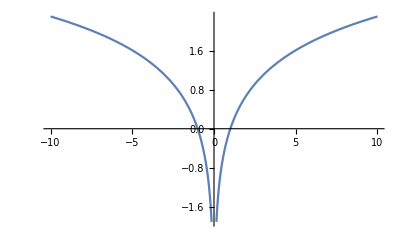

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:=1/2 Log[(a^2-x^2)/(a^2+x^2)]
D[Log[a^2-x^2],x]
Simplify[f[z]]
f'[z]//Simplify
```

-(2 x)/(a^2-x^2)

1/2 Log[(a^2-z^2)/(a^2+z^2)]

-(2 a^2 z)/(a^4-z^4)

```mathematica
f[x_]:=x/(1-Log[x-1])
f'[x]
```

x/((-1+x) (1-Log[-1+x])^2)+1/(1-Log[-1+x])

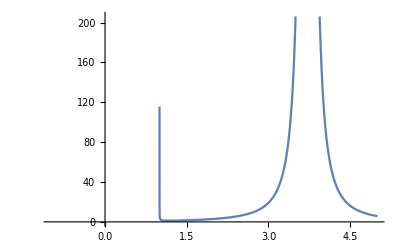

x+2 x Log[2 x]

3+2 Log[2 x]

```mathematica
Plot[x/((-1+x) (1-Log[-1+x])^2)+1/(1-Log[-1+x]),{x,-1,5.}]
```

```mathematica
Sec'[x]
```

Sec[x] Tan[x]

```mathematica
Log[0]
```

-∞

```mathematica
ClearAll[x,y,f]
f[x]:=x^2+y^2
D[y[x]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[x^2]

```mathematica
ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

ContourPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
DensityPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

RegionPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

DensityPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]
```

ContourPlot::pllim: Range specification {} ⟦ 1 ⟧ is not of the form {x, xmin, xmax}.

ContourPlot[(2 x)/(x^2+y^2),{}⟦1⟧,{}⟦2⟧]

```mathematica
Solve[y'==(2x+2y y')/(x^2+y^2),y']
```

{{y'→(2 x)/(x^2-2 y+y^2)}}